```mathematica
Directory[]
```

/home/GHo

```mathematica
SetDirectory["/home/GHo/Documents/Code/CoSSMic/Tests"]
```

/home/GHo/Documents/Code/CoSSMic/Tests

```mathematica
preddata=Import["/home/GHo/Documents/Code/CoSSMic/Tests/solarPanel1_220.csv","Table"];
```

```mathematica
{time, energy}=Transpose[preddata];
```

```mathematica
prediction = Interpolation[preddata];
```

```mathematica
prediction[300]
```

491.5

```mathematica
NIntegrate[ prediction[t],{t,0,300}]
```

71645.

```mathematica
{1451071077,2074.83},
```

```mathematica
{1451069877,0,0},
```

```mathematica
1451071077-1451069877
```

1200

```mathematica
prediction[1200]
```

2074.83

```mathematica
NIntegrate[prediction[t],{t,0,1200}]
```

1.21936×10^6

```mathematica
NIntegrate[prediction[t],{t,300,1200}]
```

1.14772×10^6

```mathematica
%24-%21
```

1.14772×10^6

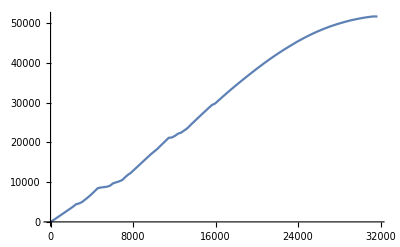

```mathematica
Plot[prediction[t],{t,0,31700}]
```

```mathematica
load1 = Import["/home/GHo/Documents/Code/CoSSMic/Tests/consumer811.csv","Table"];
```

```mathematica
load1[[-1]]
```

{6300,3616.54}

```mathematica
load2=Import["/home/GHo/Documents/Code/CoSSMic/Tests/consumer814.csv","Table"];
```

```mathematica
load2[[-1]]
```

{6900,1439}

```mathematica
load3=Import["/home/GHo/Documents/Code/CoSSMic/Tests/consumer818.csv","Table"];
```

```mathematica
load3[[-1]]
```

{3480,1385.17}

```mathematica
load4=Import["/home/GHo/Documents/Code/CoSSMic/Tests/consumer824.csv","Table"];
```

```mathematica
load4[[-1]]
```

{2700,1248.5}